# Planar3D Mesh Doubling

## Построение сеточных графиков в 2D

Указываем путь до папки с входными данными

```mathematica
folder="G:\\actualplanar\\Planar3D-MeshDoubling\\Planar3D-MeshDoubling\\Sources\\Sequential\\Sequential\\Results\\";
If[!FileExistsQ[folder], Print[Style["Папка не существует!",{Red,FontSize->24}]]]
```

Считываем параметры расчёта

```mathematica
parameters=Import[folder<>"parameters.json","RawJSON"];
(*height=parameters["mesh"]["height"];
length=parameters["mesh"]["length"];
middleH = Floor[0.5*height]+1;
middleL=Floor[0.5*length]+1;*)
size=parameters["mesh"]["height"];
middle=Floor[0.5*size]+1;
cellLength= parameters["mesh"]["cell"]["length"];
```

Задаём параметры отображения

```mathematica
(*Если True, на графике будут выводиться границы слоёв,расположенных за пределами расчётной области*)
showAllBarriers=False;
textPadding=1;
```

Указываем риски по осям графика

```mathematica
(*ticksSetVertical={
{1,N[-cellLength*(middleH-0.5)]},
{1+Floor[height/4],N[-cellLength*(middleH-0.5)*0.5]},
{1+Floor[height/2],0},
{1+Floor[3height/4],N[cellLength*(middleH-0.5)*0.5]},
{height,N[cellLength*(middleH-0.5)]}
};
ticksSetHorizontal={
{1,N[-cellLength*(middleL-0.5)]},
{1+Floor[length/4],N[-cellLength*(middleL-0.5)*0.5]},
{1+Floor[length/2],0},
{1+Floor[3length/4],N[cellLength*(middleL-0.5)*0.5]},
{length,N[cellLength*(middleL-0.5)]}
};*)
ticksSet={
{1,N[-cellLength*(middle-0.5)]},
{1+Floor[size/4],N[-cellLength*(middle-0.5)*0.5]},
{1+Floor[size/2],0},
{1+Floor[3size/4],N[cellLength*(middle-0.5)*0.5]},
{size,N[cellLength*(middle-0.5)]}
};
ticks={{ticksSet,None},{ticksSet,None}};
(*ticks={{ticksSetHorizontal,None},{ticksSetVertical,None}};*)
```

По рискам намечаем линии сетки

```mathematica
lines={};
For[
i=1;AppendTo[lines,{}];leftTicks=ticks[[1]][[1]],
i≤ Length[leftTicks],
++i,
AppendTo[lines[[Length[lines]]],leftTicks[[i]][[1]]-0.5]
]
For[
i=1;AppendTo[lines,{}];rightTicks=ticks[[1]][[1]],
i≤ Length[rightTicks],
++i,
AppendTo[lines[[Length[lines]]],rightTicks[[i]][[1]]-0.5]
]
```

Создаём массив линий–границ слоёв пласта

```mathematica
lineBarriers={};
For[
i=1; layers=parameters["layers"],
i<Length[layers],
++i,
barrierCoordinate=middle-Round[layers[ToString[i]]["y1"]/cellLength];
If[showAllBarriers||1≤barrierCoordinate && size≥barrierCoordinate,
AppendTo[lineBarriers,Line[{{1,barrierCoordinate},{size,barrierCoordinate}}]];
If[barrierCoordinate<middle ,
stress=layers[ToString[i]]["stress"],
stress=layers[ToString[i-1]]["stress"]
];
signum="";
If[stress > 0, signum="+"];
AppendTo[lineBarriers,Text[signum<>ToString[N[stress*10^-6]]<>" МПа",{1+textPadding,textPadding+barrierCoordinate}]]
]
]
barriers=Graphics[lineBarriers];
```

Задаём функции для построения и цветовую гамму

```mathematica
(*myRainbow=Function[x,Blend[{LightBlue,Green,LightGreen,White,Yellow,Orange,
RGBColor[0.6,0,0]},x]];*)
myRainbow=Function[x,Blend[{White,White,White,White,White,RGBColor[0.6,0.6,0.6],Yellow,Orange,RGBColor[0.6,0,0]},x]];
(*myRainbow=Function[x,If[0.5>x,White,ColorData["Rainbow",x]]];*)
myRainbow3D=Function[{x,y,z},ColorData["Rainbow",z]];
GlueMatrix=Function[{matrix},Transpose[Join[TakeList[Reverse[Transpose[matrix]],{Length[matrix[[1]]]-1}][[1]],Transpose[matrix]]]];
PlotMatrix= Function[{matrix,matrixName},
Show[
MatrixPlot[
GlueMatrix[matrix],PlotLabel->matrixName, FrameTicks->ticks,GridLines->lines,ColorFunction->myRainbow,PlotTheme->"Business",PlotLegends->Automatic,ImageSize->Large],
barriers]
];
```

Загружаем данные для построения

```mathematica
(*timeStep=59;
rightFlow=Import[folder<>"Flows/right_"<>ToString[timeStep]<>"_m.txt", "Table"];
leftFlow=Import[folder<>"Flows/left_"<>ToString[timeStep]<>"_m.txt", "Table"];
upFlow=Import[folder<>"Flows/up_"<>ToString[timeStep]<>"_m.txt", "Table"];
downFlow=Import[folder<>"Flows/down_"<>ToString[timeStep]<>"_m.txt", "Table"];
opening=Import[folder<>"Opening/"<>ToString[timeStep]<>"_m.txt", "Table"];*)
```

```mathematica
opening=Import[folder<>"opening_m.txt", "Table"];
fracture=Import[folder<>"fracture_m.txt", "Table"];
openingAtTime=Function[t,Import[folder<>"Opening/"<>ToString[t]<>"_m.txt", "Table"]];
totalTime=Length[FileNames["*",folder<>"Opening/"]];
```

Выводим время последнего запуска

```mathematica
If[!FileExistsQ[folder], Print[Style["Папка не существует!",{Red,FontSize->24}]]]
Print[Style["Время последнего запуска:" Style[DateString[],Orange],{FontSize->24}]]
```

Время последнего запуска: Tue 30 Oct 2018 17:29:45

Строим графики

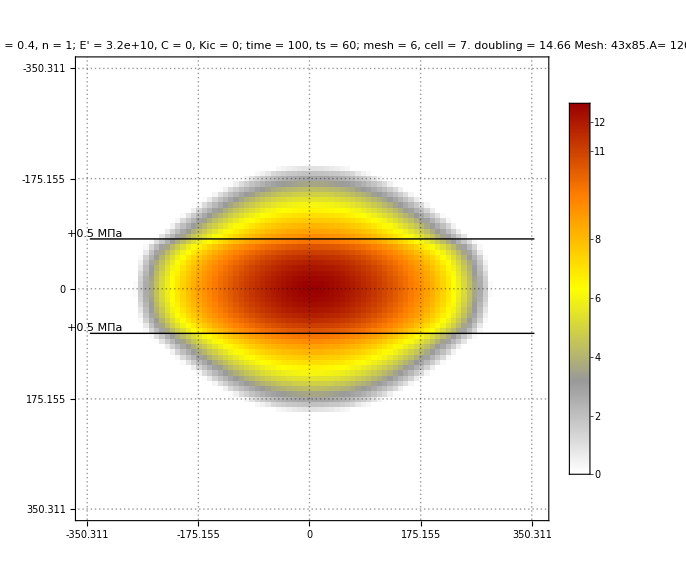

```mathematica
(*GridBox[
{{PlotMatrix[upFlow, "Скорость объёмного подвода по вертикали от центра"],
PlotMatrix[downFlow, "Скорость объёмного подвода по вертикали к центру"]},
{PlotMatrix[leftFlow, "Скорость объёмного подвода по горизонтали от центра"],
PlotMatrix[rightFlow, "Скорость объёмного подвода по горизонтали к центру"]}}
]//DisplayForm*)
PlotMatrix[opening, " Q = 0.16, mu = 0.4, n = 1;
  E' = 3.2e+10, C = 0, Kic = 0;
  time = 100, ts = 60;
  mesh = 6, cell = 7.
doubling = 14.66
Mesh: 43x85.A= 1200
"]
```

Part::partd: Part specification openingDouble⟦16⟧ is longer than depth of object.

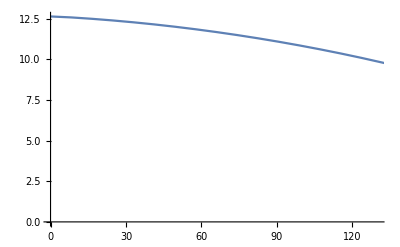

```mathematica
Show[
ListLinePlot[Table[{cellLength*(i-1),opening[[middle]][[i]]},{i,1,Length[opening[[middle]]],1}],PlotRange->{{0,130},All}],ListLinePlot[Table[{cellLengthDouble*(i-1),openingDouble[[16]][[i]]},{i,1,Length[openingDouble[[16]]],1}],PlotRange->{{0,130},All},PlotStyle->Green]
]
```

```mathematica
MatrixForm[fracture[[Length[fracture]]]]
```

(100
0.26481
268.419
191.598)

```mathematica
MatrixForm[fracture[[Length[fracture]]]]
```

(100
0.26481
268.419
191.598)

```mathematica
MatrixPlot[openingDouble]
```

MatrixPlot::mat0: Argument openingDouble at position 1 is not a matrix.

MatrixPlot[openingDouble]

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Transpose::list: List expected at position 2 in Transpose[$Failed,$Failed].

MatrixPlot::mat0: Argument Transpose[Transpose[$Failed,$Failed]] at position 1 is not a matrix.

Show::gcomb: Could not combine the graphics objects in Show[MatrixPlot[Transpose[Transpose[$Failed,$Failed]],PlotLabel→Раскрытие,FrameTicks→{{{{1,-350.311},«3»,{85,«19»}},None},«1»},«1»,«1»,«9»→…s,PlotLegends→Automatic,ImageSize→Large],].

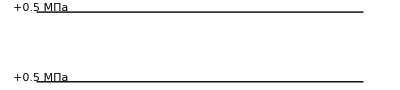
Show[MatrixPlot[Transpose[Transpose[$Failed,$Failed]],PlotLabel→Раскрытие,FrameTicks→{{{{1,-350.311},{22,-175.155},{43,0},{64,175.155},{85,350.311}},None},{{{1,-350.311},{22,-175.155},{43,0},{64,175.155},{85,350.311}},None}},GridLines→{{0.5,21.5,42.5,63.5,84.5},{0.5,21.5,42.5,63.5,84.5}},ColorFunction→Function[x,Blend[{White,White,White,White,White,RGBColor[0.6, 0.6, 0.6],Yellow,Orange,RGBColor[0.6, 0, 0]},x]],PlotTheme→Business,PlotLegends→Automatic,ImageSize→Large],-Graphics-]

```mathematica
PlotMatrix[openingAtTime[120], "Раскрытие"]
```

```mathematica
(*./run.sh --mesh-size=12 --barriers=./InitialConditions/barriers13.txt --E=25 --time=60 --save-steps*)
```

```mathematica
upFlowAtTime=Function[t,Import[folder<>"Flows/up_"<>ToString[t]<>"_m.txt", "Table"]];
downFlowAtTime=Function[t,Import[folder<>"Flows/down_"<>ToString[t]<>"_m.txt", "Table"]];
```

```mathematica
plots=Table[PlotMatrix[openingAtTime[t], "Раскрытие, кадр №" <>ToString[t]],{t,1,587,10}];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Transpose::list: List expected at position 2 in Transpose[$Failed,$Failed].

MatrixPlot::mat0: Argument Transpose[Transpose[$Failed,$Failed]] at position 1 is not a matrix.

Show::gcomb: Could not combine the graphics objects in Show[MatrixPlot[Transpose[Transpose[$Failed,$Failed]],PlotLabel→Раскрытие, кадр №1,«4»,PlotLegends→Automatic,ImageSize→Large],].

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Transpose::list: List expected at position 2 in Transpose[$Failed,$Failed].

MatrixPlot::mat0: Argument Transpose[Transpose[$Failed,$Failed]] at position 1 is not a matrix.

Show::gcomb: Could not combine the graphics objects in Show[MatrixPlot[Transpose[Transpose[$Failed,$Failed]],PlotLabel→Раскрытие, кадр №11,«4»,PlotLegends→Automatic,ImageSize→Large],].

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::list: List expected at position 2 in Transpose[$Failed,$Failed].

General::stop: Further output of Transpose::list will be suppressed during this calculation.

MatrixPlot::mat0: Argument Transpose[Transpose[$Failed,$Failed]] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[MatrixPlot[Transpose[Transpose[$Failed,$Failed]],PlotLabel→Раскрытие, кадр №21,«4»,PlotLegends→Automatic,ImageSize→Large],].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
animation=ListAnimate[plots]
```

```mathematica
Export["~/Desktop/anim.gif",animation]
```

Export::nodir: Directory C:\Users\Nikita\Documents\~\Desktop\ does not exist.

Export::noopen: Cannot open ~/Desktop/anim.gif.

$Failed

```mathematica
Create gif
```

Create gif

```mathematica
ListPlot3D[
GlueMatrix[opening],PlotLabel->"Раскрытие",ColorFunction->myRainbow3D,PlotTheme->"Business",PlotLegends->Automatic,ImageSize->Large,ViewPoint->Top,BoxStyle->Dotted,PlotLegends->Automatic ]
```

-Graphics3D-

```mathematica
lineBarriers
```

{Line[{{1,52},{85,52}}],Text[+0.5 МПа,{2,53}],Line[{{1,34},{85,34}}],Text[+0.5 МПа,{2,35}]}

```mathematica
barriersPlots3D=Table[ListPlot3D[opening,PlotStyle->None,Mesh->{{0,0},{line3DBarriers[[i]],0}},MeshStyle->Directive[Thick,Dashed,White]],{i,1,Length[line3DBarriers],1}];
```

```mathematica
barriersPlots3D
```

{}

```mathematica
line3DBarriers={};
For[
i=1; layers=parameters["layers"],
i<Length[layers],
++i,
barrierCoordinate=middle-Round[layers[ToString[i]]["y1"]/cellLength];
If[showAllBarriers||1≤barrierCoordinate && size≥barrierCoordinate,
AppendTo[line3DBarriers,barrierCoordinate]
]
]
```

```mathematica
line3DBarriers
```

{52,34}